```mathematica
ClearAll["Global`*"];
suciastky={r1->1,r2->1,c1->1,c2->1};
tmax=10;
uz[t_]:=1
rovnice = 
{

0==iu[t]+ir1[t],
ir1[t]==ic2[t]+ic1[t],
ic2[t]==ir2[t],

uz[t]==u1[t],
u1[t]-u2[t]==r1*ir1[t],
u3[t]==r2*ir2[t],
ic1[t]==c1*u2'[t],
ic2[t]==c2*(u2'[t]-u3'[t]),

u2[0]==0,
u3[0]==0

};
premenne={u1[t],u2[t],u3[t],iu[t],ir1[t],ir2[t],ic1[t],ic2[t]};
riesenie=NDSolve[rovnice/.suciastky,premenne,{t,0,tmax}];
Plot[{uz[t],u2[t]/.riesenie,u3[t]/.riesenie},{t,0,tmax}]
```

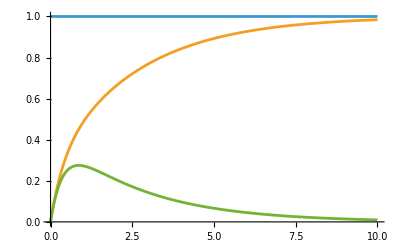

```mathematica
Limit[u2[t]/.riesenie,t->∞]
Limit[u3[t]/.riesenie,t->∞]
```

lim_(t→∞) {InterpolatingFunction[…][t]}

lim_(t→∞) {InterpolatingFunction[…][t]}